```mathematica
α=1;
β=2;
γ=3;
p[x_]=(x-α)(x-β)(x-γ)
```

(-3+x) (-2+x) (-1+x)

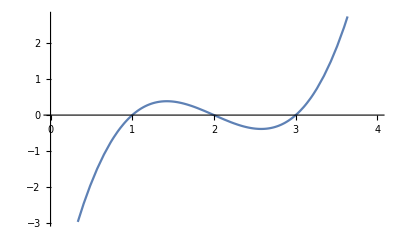

```mathematica
Plot[p[x],{x,0,4}]
```

```mathematica
RecurrenceTable[{x[n+1]==x[n]-p[x[n]]/p'[x[n]],x[0]==Evaluate[x/.s13]},x[n],{n,0,15}]
```

{2.44721,1.55279,2.44721,1.55279,2.44721,1.55279,2.44721,1.55278,2.44723,1.5527,2.44771,1.5498,2.4656,1.42264,-10024.6,-6682.42}

```mathematica
crits=Solve[p'[x]==0,x];
s1=FindRoot[Evaluate[x/.crits⟦1⟧]==x-p[x]/p'[x],{x,x/.crits⟦1⟧,x/.crits⟦2⟧}]
s2=FindRoot[Evaluate[x/.s1]==x-p[x]/p'[x],{x,x/.crits⟦1⟧,x/.crits⟦2⟧}]
s3=FindRoot[Evaluate[x/.s2]==x-p[x]/p'[x],{x,x/.crits⟦1⟧,x/.crits⟦2⟧}]
s4=FindRoot[Evaluate[x/.s3]==x-p[x]/p'[x],{x,x/.crits⟦1⟧,x/.crits⟦2⟧}]
s5=FindRoot[Evaluate[x/.s4]==x-p[x]/p'[x],{x,x/.crits⟦1⟧,x/.crits⟦2⟧}]
s6=FindRoot[Evaluate[x/.s5]==x-p[x]/p'[x],{x,x/.crits⟦1⟧,x/.crits⟦2⟧}]
s7=FindRoot[Evaluate[x/.s6]==x-p[x]/p'[x],{x,x/.crits⟦1⟧,x/.crits⟦2⟧}]
s8=FindRoot[Evaluate[x/.s7]==x-p[x]/p'[x],{x,x/.crits⟦1⟧,x/.crits⟦2⟧}]
s9=FindRoot[Evaluate[x/.s8]==x-p[x]/p'[x],{x,x/.crits⟦1⟧,x/.crits⟦2⟧}]
s10=FindRoot[Evaluate[x/.s9]==x-p[x]/p'[x],{x,x/.crits⟦1⟧,x/.crits⟦2⟧}]
s11=FindRoot[Evaluate[x/.s10]==x-p[x]/p'[x],{x,x/.crits⟦1⟧,x/.crits⟦2⟧}]
s12=FindRoot[Evaluate[x/.s11]==x-p[x]/p'[x],{x,x/.crits⟦1⟧,x/.crits⟦2⟧}]
s13=FindRoot[Evaluate[x/.s12]==x-p[x]/p'[x],{x,x/.crits⟦1⟧,x/.crits⟦2⟧}]
```

{x→2.4656}

{x→1.5498}

{x→2.44771}

{x→1.5527}

{x→2.44723}

{x→1.55278}

{x→2.44721}

{x→1.55279}

{x→2.44721}

{x→1.55279}

{x→2.44721}

{x→1.55279}

{x→2.44721}

```mathematica
FixedPointList[#-p[#]/p'[#]&,x/.s6]//Length
```

72